Analysis of transition frequencies for △p=0 with △m = -1,0,1 and different initial and final m scenarios

Filenames for △m=-1,0,1 with transitions of the form △p=0

```mathematica
Scenario2="C:\\University\\Honours\\Formal delta m experiments\\Scenario 2.txt";
```

```mathematica
Scenario4="C:\\University\\Honours\\Formal delta m experiments\\Scenario 4.txt";
```

```mathematica
Scenario6="C:\\University\\Honours\\Formal delta m experiments\\Scenario 6.txt";
```

```mathematica
Scenario8 = "C:\\University\\Honours\\Formal delta m experiments\\Scenario 8.txt";
```

```mathematica
Scenario9 = "C:\\University\\Honours\\Formal delta m experiments\\Scenario 9.txt"
```

C:\University\Honours\Formal delta m experiments\Scenario 9.txt

```mathematica
Scenario13 = "C:\\University\\Honours\\Formal delta m experiments\\Scenario 13.txt"
```

C:\University\Honours\Formal delta m experiments\Scenario 13.txt

```mathematica
Scenario14 = "C:\\University\\Honours\\Formal delta m experiments\\Scenario 14.txt"
```

C:\University\Honours\Formal delta m experiments\Scenario 14.txt

```mathematica
datalist=ReadList[Scenario2];
```

Functions ReadFile, ReadFileB reads Transition frequencies as a function of principle quantum number <n>

```mathematica
ReadFile[min_, max_,opt_:1]:=(nvals=Range[min, max, 5]; lists=Map[ReadFileB ,nvals];
Return[lists])
```

```mathematica
ReadFileB[nval_]:=(posn=Position[datalist, {nval,_,_,_,_,_,_}];e=Extract[datalist, posn]; Return[GetLastLog10@@@e])
```

Function GetLast* & GetLog* operate on lists to extract the data

```mathematica
GetLast[_,_,_,_,_,_,last_]:=last
```

```mathematica
GetLastLog10[_,_,_,_,_,_,last_]:=Log10[last]
```

```mathematica
GetPLast[in_,il_,_,_,_,_, last_]:={(in-il),last }
```

```mathematica
GetPLog10[in_,il_,_,_,_,_, last_]:={(in-il),Log[last] }
```

Scenario 2: △m = 0, △l = -1, △p = 0, mi = mf = 0

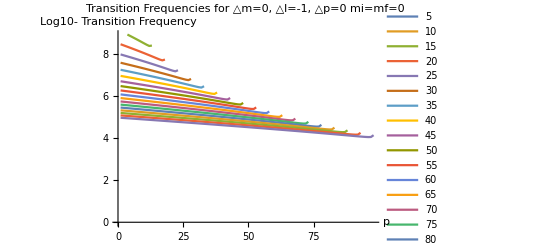

```mathematica
ListLinePlot[ReadFile[5,100], PlotLegends->Table[i,{i, 5, 100, 5}],AxesLabel->{p, "Log10-\nTransition \nFrequency"},PlotLabel->"Transition Frequencies for △m=0, △l=-1, △p=0 mi=mf=0"]
```

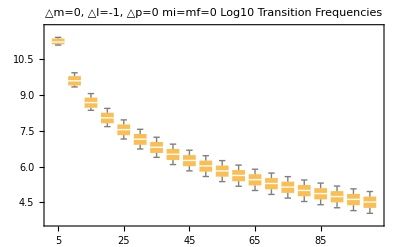

```mathematica
BoxWhiskerChart[DeleteCases[ReadFile[5,100], -Infinity,2], "Outliers",ChartLabels->Table[i, {i,5,100, 5}],PlotLabel->"△m=0, △l=-1, △p=0 mi=mf=0\nLog10 Transition Frequencies"]
```

```mathematica
list=DeleteCases[GetPLog10@@@datalist, -Infinity, 2];
```

```mathematica
data=Table[Flatten[Last/@Cases[list, {i,_} , i]], {i, 3, 60}];
```

```mathematica
means=Mean/@data;
```

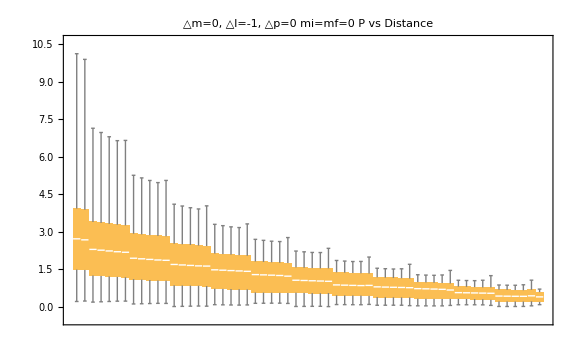

```mathematica
BoxWhiskerChart[Sqrt[Power[data-means, 2]],PlotLabel->"△m=0, △l=-1, △p=0 mi=mf=0\nP vs Distance"]
```

Scenario 4: △m = -1, △l = -1, △p = 0, mi = 0 mf = -1

```mathematica
datalist=ReadList[Scenario4];
```

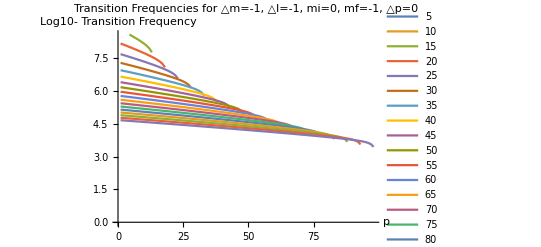

```mathematica
ListLinePlot[ReadFile[5,100], PlotLegends->Table[i,{i, 5, 100, 5}],AxesLabel->{p, "Log10-\nTransition \nFrequency"},PlotLabel->"Transition Frequencies for △m=-1, △l=-1, mi=0, mf=-1, △p=0"]
```

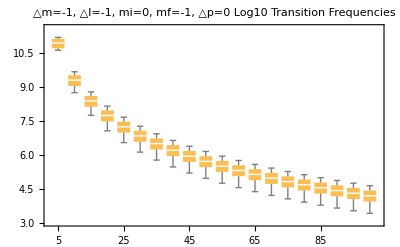

```mathematica
BoxWhiskerChart[DeleteCases[ReadFile[5,100], -Infinity,2], "Outliers",ChartLabels->Table[i, {i,5,100, 5}],PlotLabel->"△m=-1, △l=-1, mi=0, mf=-1, △p=0\nLog10 Transition Frequencies"]
```

```mathematica
list2=DeleteCases[GetPLog10@@@datalist, -Infinity, 2];
```

```mathematica
data2=Table[Flatten[Last/@Cases[list2, {i,_} , i]], {i, 3, 60}];
```

```mathematica
means2=Mean/@data2;
```

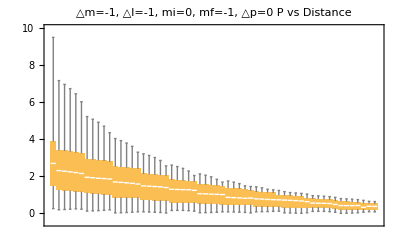

```mathematica
BoxWhiskerChart[Sqrt[Power[data2-means2, 2]],PlotLabel->"△m=-1, △l=-1, mi=0, mf=-1, △p=0\nP vs Distance"]
```

Scenario 6: △m=-1 with mi = li and mf = lf, △l=-1, △p = 0

```mathematica
datalist=ReadList[Scenario6];
```

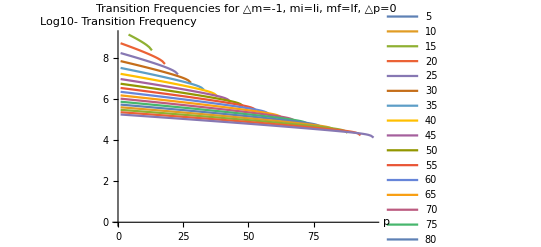

```mathematica
ListLinePlot[ReadFile[5,100], PlotLegends->Table[i,{i, 5, 100, 5}],AxesLabel->{p, "Log10-\nTransition \nFrequency"},PlotLabel->"Transition Frequencies for △m=-1, mi=li, mf=lf, △p=0"]
```

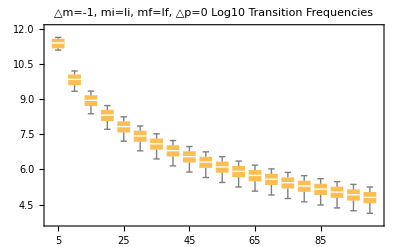

```mathematica
BoxWhiskerChart[DeleteCases[ReadFile[5,100], -Infinity,2], "Outliers",ChartLabels->Table[i, {i,5,100, 5}],PlotLabel->"△m=-1, mi=li, mf=lf, △p=0\nLog10 Transition Frequencies"]
```

```mathematica
list3=DeleteCases[GetPLog10@@@datalist, -Infinity, 2];
```

```mathematica
data3=Table[Flatten[Last/@Cases[list3, {i,_} , i]], {i, 3, 60}];
```

```mathematica
means3=Mean/@data3;
```

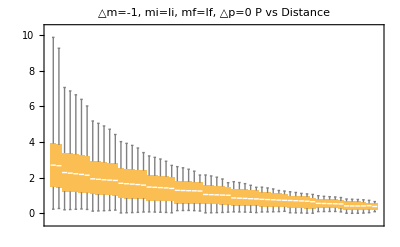

```mathematica
BoxWhiskerChart[Sqrt[Power[data3-means3, 2]],PlotLabel->"△m=-1, mi=li, mf=lf, △p=0\nP vs Distance"]
```

```mathematica
Scenario 8: △m=+1 with mi = -li and mf = -lf, △l=-1, △p = 0
```

Syntax::sntxf: "Scenario 8" cannot be followed by 
    ": △m=+1 with mi = -li and mf = -lf, △l=-1,
      △p = 0".

Syntax::sntxf: " △m=+1 with mi = -li a" cannot be followed by 
    "nd mf = -lf, △l=-1, △p = 0".

Syntax::sntxf: "" cannot be followed by 
    "iangle]m=+1 with mi = -li and mf = -lf, △l=-1,
      △p = 0".

0

```mathematica
datalist=ReadList[Scenario8];
```

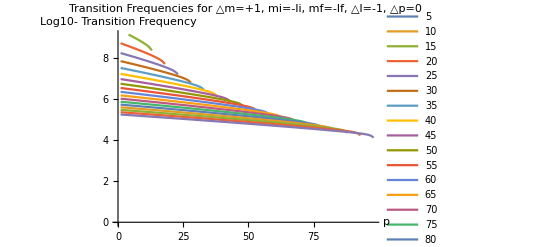

```mathematica
ListLinePlot[ReadFile[5,100], PlotLegends->Table[i,{i, 5, 100, 5}],AxesLabel->{p, "Log10-\nTransition \nFrequency"},PlotLabel->"Transition Frequencies for △m=+1, mi=-li, mf=-lf, △l=-1, △p=0"]
```

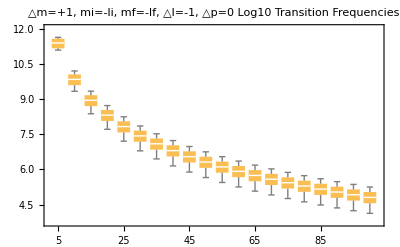

```mathematica
BoxWhiskerChart[DeleteCases[ReadFile[5,100], -Infinity,2], "Outliers",ChartLabels->Table[i, {i,5,100, 5}],PlotLabel->"△m=+1, mi=-li, mf=-lf, △l=-1, △p=0\nLog10 Transition Frequencies"]
```

```mathematica
list3=DeleteCases[GetPLog10@@@datalist, -Infinity, 2];
```

```mathematica
data3=Table[Flatten[Last/@Cases[list3, {i,_} , i]], {i, 3, 60}];
```

```mathematica
means3=Mean/@data3;
```

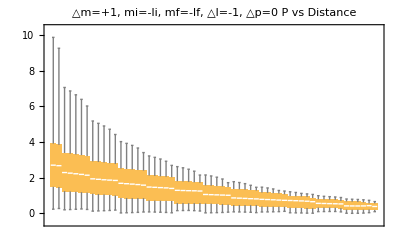

```mathematica
BoxWhiskerChart[Sqrt[Power[data3-means3, 2]],PlotLabel->"△m=+1, mi=-li, mf=-lf, △l=-1, △p=0\nP vs Distance"]
```

Scenario 9: △m=0 with mi = mf = ni-5, △l=-1, △p = 0

```mathematica
datalist=ReadList[Scenario9];
```

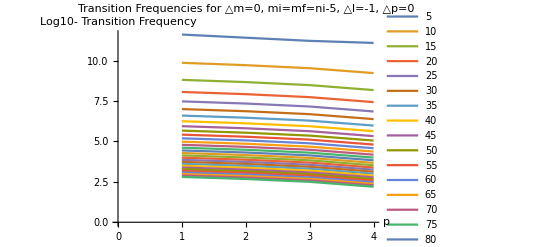

```mathematica
ListLinePlot[ReadFile[5,150], PlotLegends->Table[i,{i, 5, 150, 5}],AxesLabel->{p, "Log10-\nTransition \nFrequency"},PlotLabel->"Transition Frequencies for △m=0, mi=mf=ni-5, △l=-1, △p=0"]
```

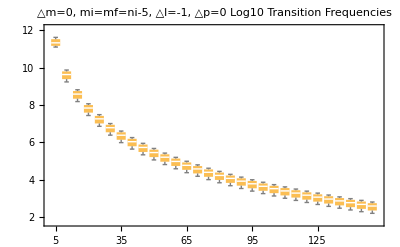

```mathematica
BoxWhiskerChart[DeleteCases[ReadFile[5,150], -Infinity,2], "Outliers",ChartLabels->Table[i, {i,5,150, 5}],PlotLabel->"△m=0, mi=mf=ni-5, △l=-1, △p=0\nLog10 Transition Frequencies"]
```

```mathematica
list2=DeleteCases[GetPLog10@@@datalist, -Infinity, 2];
```

```mathematica
data2=Table[Flatten[Last/@Cases[list2, {i,_} , i]], {i, 3, 60}];
```

```mathematica
means2=Mean/@data2;
```

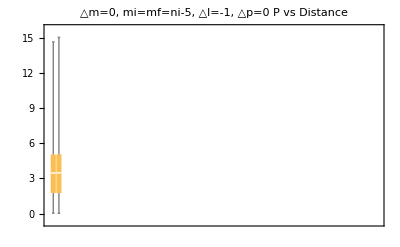

```mathematica
BoxWhiskerChart[Sqrt[Power[data2-means2, 2]],PlotLabel->"△m=0, mi=mf=ni-5, △l=-1, △p=0\nP vs Distance"]
```

Scenario 13: △m=-1 with mi = ni-5, mf = ni-6, △l=-1, △p = 0

```mathematica
datalist=ReadList[Scenario13];
```

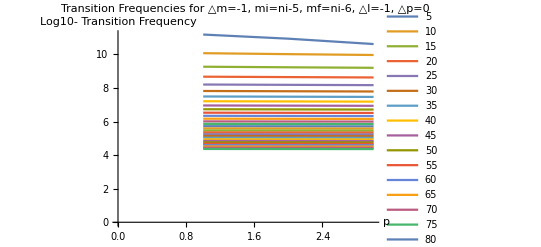

```mathematica
ListLinePlot[ReadFile[5,150], PlotLegends->Table[i,{i, 5, 150, 5}],AxesLabel->{p, "Log10-\nTransition \nFrequency"},PlotLabel->"Transition Frequencies for △m=-1, mi=ni-5, mf=ni-6, △l=-1, △p=0"]
```

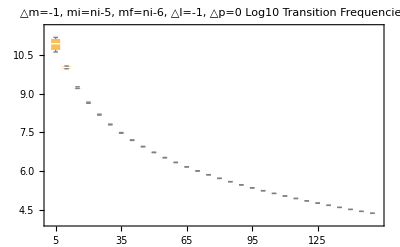

```mathematica
BoxWhiskerChart[DeleteCases[ReadFile[5,150], -Infinity,2], "Outliers",ChartLabels->Table[i, {i,5,150, 5}],PlotLabel->"△m=-1, mi=ni-5, mf=ni-6, △l=-1, △p=0\nLog10 Transition Frequencies"]
```

```mathematica
list2=DeleteCases[GetPLog10@@@datalist, -Infinity, 2];
```

```mathematica
data2=Table[Flatten[Last/@Cases[list2, {i,_} , i]], {i, 3, 60}];
```

```mathematica
means2=Mean/@data2;
```

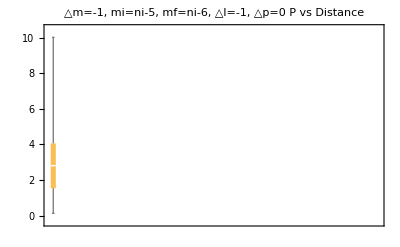

```mathematica
BoxWhiskerChart[Sqrt[Power[data2-means2, 2]],PlotLabel->"△m=-1, mi=ni-5, mf=ni-6, △l=-1, △p=0\nP vs Distance"]
```

Scenario 14: △m=+1 with mi = ni-5, mf = ni-4, △l=-1, △p = 0

```mathematica
datalist=ReadList[Scenario14];
```

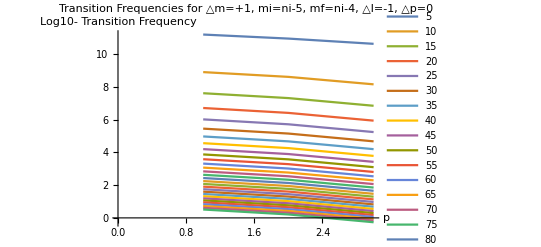

```mathematica
ListLinePlot[ReadFile[5,150], PlotLegends->Table[i,{i, 5, 150, 5}],AxesLabel->{p, "Log10-\nTransition \nFrequency"},PlotLabel->"Transition Frequencies for △m=+1, mi=ni-5, mf=ni-4, △l=-1, △p=0"]
```

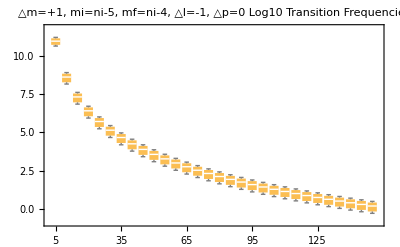

```mathematica
BoxWhiskerChart[DeleteCases[ReadFile[5,150], -Infinity,2], "Outliers",ChartLabels->Table[i, {i,5,150, 5}],PlotLabel->"△m=+1, mi=ni-5, mf=ni-4, △l=-1, △p=0\nLog10 Transition Frequencies"]
```

```mathematica
list2=DeleteCases[GetPLog10@@@datalist, -Infinity, 2];
```

```mathematica
data2=Table[Flatten[Last/@Cases[list2, {i,_} , i]], {i, 3, 60}];
```

```mathematica
means2=Mean/@data2;
```

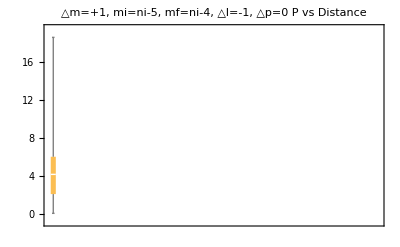

```mathematica
BoxWhiskerChart[Sqrt[Power[data2-means2, 2]],PlotLabel->"△m=+1, mi=ni-5, mf=ni-4, △l=-1, △p=0\nP vs Distance"]
```